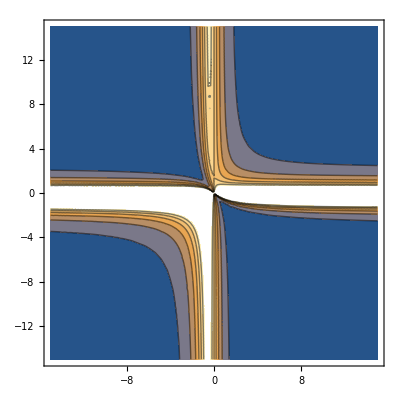

```mathematica
ContourPlot[(y^2+2x y+ 4x^2/3)/(x^2y^2+y^2+x^2/5+x y^2+2x^2y/3 +x y/2), {x,-15,15},{y,-15,15}]
```

```mathematica
MaxValue[(y^2+2x y+ 4x^2/3)/(x^2y^2+y^2+x^2/5+x y^2+2x^2y/3 +x y/2), {x,y}]
```

-4/43 (-83-2 √1561)

```mathematica
ArgMax[(y^2+2x y+ 4x^2/3)/(x^2y^2+y^2+x^2/5+x y^2+2x^2y/3 +x y/2), {x,y}]
```

{12.9182487550461370118487223,-0.32091243775230685059243611}

```mathematica
N[MaxValue[(b^2 + 2 b c +4c^2 /3)/(a^2+b^2 + c^2/5 + a b + 2 a c /3 + b c/2), {a,b,c}]]
```

15.0715

```mathematica
Eigenvalues[{{{0,0,0},{0,1,1},{0,1,4/3}}, {{1, 1/2, 1/3},{1/2, 1/3, 1/4},{1/3, 1/4, 1/5}}}]
```

{60,12,0}

```mathematica
MaxValue[4/(x^2 + y^2/3 +1/5 + x y +2 x /3 + y /2), {x,y}]
```

720

```mathematica
f[x_, y_]:=(y^2+2x y+ 4x^2/3)/(x^2y^2+y^2+x^2/5+x y^2+2x^2y/3 +x y/2)
```

```mathematica
f[12.918, -0.3209]
```

15.0715

```mathematica
MaxValue[(y^2+2 y+ 4/3)/(x^2+y^2+x y+2x/3 + y/2 + 1/5), {x,y}]
```

-4/43 (-83-2 √1561)

```mathematica
N1[x_]:= x/h;
N2[x_]:= 1 - x/h;
```

```mathematica
Integrate[N1'[x] N1'[x], {x, 0, h}]
Integrate[N2'[x] N2'[x], {x, 0, h}]
Integrate[N1'[x] N2'[x], {x, 0, h}]
```

1/h

1/h

-1/h

```mathematica
Integrate[N1[x] N1[x], {x, 0, h}]
Integrate[N2[x] N2[x], {x, 0, h}]
Integrate[N1[x] N2[x], {x, 0, h}]
```

h/3

h/3

h/6

```mathematica
Eigenvalues[{{{1, -1},{-1 , 1}} , (1/6){{2, 1},{1, 2}}}    ]
```

{12,0}

```mathematica
M1[x_]:= 2 (x/h -1) (x/h - 1/2)
M2[x_]:= 4x/h (1-x/h)
M3[x_] := 2x/h (x/h - 1/2)
```

```mathematica
Integrate[M1'[x] M1'[x], {x, 0, h}]
Integrate[M2'[x] M2'[x], {x, 0, h}]
Integrate[M3'[x] M3'[x], {x, 0, h}]
Integrate[M1'[x] M2'[x], {x, 0, h}]
Integrate[M1'[x] M3'[x], {x, 0, h}]
Integrate[M3'[x] M2'[x], {x, 0, h}]
```

7/(3 h)

16/(3 h)

7/(3 h)

-8/(3 h)

1/(3 h)

-8/(3 h)

```mathematica
Integrate[M1[x] M1[x], {x, 0, h}]
Integrate[M2[x] M2[x], {x, 0, h}]
Integrate[M3[x] M3[x], {x, 0, h}]
Integrate[M1[x] M2[x], {x, 0, h}]
Integrate[M1[x] M3[x], {x, 0, h}]
Integrate[M3[x] M2[x], {x, 0, h}]
```

(2 h)/15

(8 h)/15

(2 h)/15

h/15

-h/30

h/15

```mathematica
Eigenvalues[{(1/3){{7, -8, 1},{-8, 16, -8},{1, -8, 7}}, (1/30){{4, 2, -1},{2, 16, 2},{-1, 2, 4}}}]
```

{60,12,0}

```mathematica
Integrate[M1''[x] M1''[x], {x, 0, h}]
Integrate[M2''[x] M2''[x], {x, 0, h}]
Integrate[M3''[x] M3''[x], {x, 0, h}]
Integrate[M1''[x] M2''[x], {x, 0, h}]
Integrate[M1''[x] M3''[x], {x, 0, h}]
Integrate[M3''[x] M2''[x], {x, 0, h}]
```

16/h^3

64/h^3

16/h^3

-32/h^3

16/h^3

-32/h^3

```mathematica
Eigenvalues[{{{16, -32, 16},{-32, 64, -32},{16, -32, 16}}, (1/30){{4, 2, -1},{2, 16, 2},{-1, 2, 4}}}]
```

{0,0,0}